Lõikekohad:

{{x→0.},{x→-2.27886},{x→6.21234}}

Graafik:

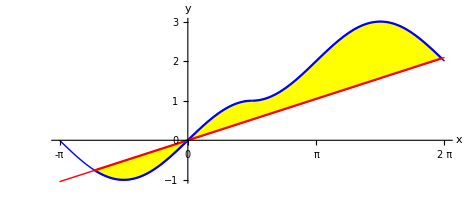

Kollase osa pindala:

5.63321

8. oli liiga raske, et midagi kirja panna

```mathematica
(* Kontrolltöö
  Siim Erik Pugal
  179411YAFB      *)
fn[x_]:=Module[{f},If[x≤π/2,f=Sin[x],f=2-Cos[x-π/2]]]
punktid=Table[{{x,0},{x,fn[x]}},{x,π/2,2 π,π/2}];
graafik=Plot[fn[x],{x,-π,2 π},PlotStyle->{Blue,Thick},AspectRatio->Automatic,Ticks->{{-π,-π/2,0,π/2,π,(3 π)/2,2 π},Automatic},GridLines->{{-π,-π/2,0,π/2,π,(3 π)/2,2 π},{-1,1,2,3}},AxesStyle->{{Thickness[0.004],Arrowheads[{0,0.035}],Orange},{Thickness[0.004],Arrowheads[{0,0.035}],Orange}},AxesLabel->{"x","y"}];
f2=1/3*x;
graafik2=Plot[{f2},{x,-π,2π},PlotStyle->{Red,Thick}];
"Lõikekohad:"
rajad=FindInstance[fn[x]==f2,x,Reals,3]//N   (*Rajad/Lõikekohad*)
rajad[[1]];    (*Proov: Esimene element raja listist*)
ala1=Plot[{fn[x],f2},{x,0,6.212344553018566},
PlotStyle->{Blue,Red},Filling->{1->{2}},
FillingStyle->Yellow];
ala2=Plot[{fn[x],f2},{x,-2.2788626600758284,0},
PlotStyle->{Blue,Red},Filling->{1->{2}},
FillingStyle->Yellow];
"Graafik:"
Show[graafik,graafik2,ala1,ala2]
S1=NIntegrate[fn[x]-f2,{x,0,6.212344553018566},Method->{"NewtonCotesRule","Order"->2}]// Quiet ;
S2=NIntegrate[f2-fn[x],{x,-2.2788626600758284,0},Method->{"NewtonCotesRule","Order"->2}]// Quiet; 
"Kollase osa pindala:"
S =S1+S2
"8. oli liiga raske, et midagi kirja panna"
```